```mathematica
%%Gaussian trial solution%%
```

```mathematica
%%Ground state%%
```

```mathematica
A0=√(1/(√π a[t]));
ψ1[x_,t_]=Exp[-x^2/(2 a[t]^2)+ⅈ b[t] x^2]A0 HermiteH[0,x/a[t]];
ψ2[x_,t_]=Exp[-x^2/(2 a[t]^2)-ⅈ b[t] x^2]A0 HermiteH[0,x/a[t]];
```

```mathematica
Integrate[ψ1[x,t]ψ2[x,t],{x,-∞,∞},Assumptions->a[t]>0]
```

1

```mathematica
wave[x_,t_]=ψ1[x,t]ψ2[x,t];
```

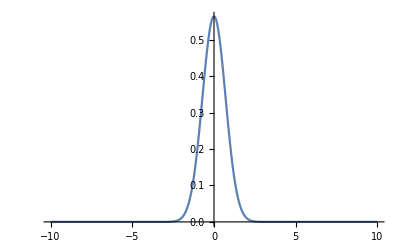

1/(√π)

```mathematica
a[t_]=1;
Plot[wave[x,t],{x,-10,10},PlotRange->All]
MaxValue[wave[x,t],x]
```

```mathematica
wave[1,t]
```

1/(ⅇ √π)

```mathematica
N[Solve[wave[x,t]==1/(2 √π),x,Reals]]
```

{{x→-0.832555},{x→0.832555}}

```mathematica
%%First excited state%%
```

```mathematica
A1=√(1/(√π 2 a[t]));
ψ1[x_,t_]=Exp[-x^2/(2 a[t]^2)+ⅈ b[t] x^2]A1 HermiteH[1,x/a[t]];
ψ2[x_,t_]=Exp[-x^2/(2 a[t]^2)-ⅈ b[t] x^2]A1 HermiteH[1,x/a[t]];
```

```mathematica
wave[x_,t_]=ψ1[x,t]ψ2[x,t];
```

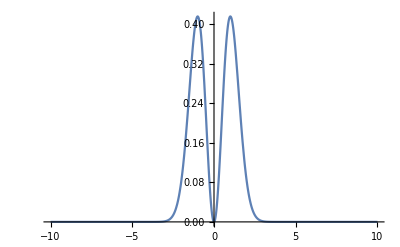

2/(ⅇ √π)

```mathematica
a[t_]=1;
Plot[wave[x,t],{x,-10,10},PlotRange->All]
MaxValue[wave[x,t],x]
```

```mathematica
wave[√3,t]
```

6/(ⅇ^3 √π)

```mathematica
N[6/(ⅇ^3 √π)]
```

0.168536

```mathematica
N[Solve[wave[x,t]==6/(ⅇ^3 √π),x,Reals]]
```

{{x→-1.73205},{x→1.73205},{x→-0.422564},{x→0.422564}}

```mathematica
%%Second excited state%%
```

```mathematica
A2=√(1/(√π 2^2 2a[t]));
ψ1[x_,t_]=Exp[-x^2/(2 a[t]^2)+ⅈ b[t] x^2]A2 HermiteH[2,x/a[t]];
ψ2[x_,t_]=Exp[-x^2/(2 a[t]^2)-ⅈ b[t] x^2]A2 HermiteH[2,x/a[t]];
```

```mathematica
%%Forth excited state%%
```

```mathematica
A4=√(1/(√π 2^4 4!a[t]));
ψ1[x_,t_]=Exp[-x^2/(2 a[t]^2)+ⅈ b[t] x^2]A4 HermiteH[4,x/a[t]];
ψ2[x_,t_]=Exp[-x^2/(2 a[t]^2)-ⅈ b[t] x^2]A4 HermiteH[4,x/a[t]];
```

```mathematica
%% Nth excited state%%
```

```mathematica
n=3;
An=√(1/(√π 2^n n!a[t]));
ψ1[x_,t_]=Exp[-x^2/(2 a[t]^2)+ⅈ b[t] x^2]An HermiteH[n,x/a[t]];
ψ2[x_,t_]=Exp[-x^2/(2 a[t]^2)-ⅈ b[t] x^2]An HermiteH[n,x/a[t]];
```

```mathematica
Integrate[ψ2[x,t]ψ1[x,t],{x,-∞,∞},Assumptions->a[t]>0]
```

1

```mathematica
b[t]chirp;c[t]slope;ϕ[t]phase
```

```mathematica
HermiteH[2,x/a[t]]
```

-2+(4 x^2)/a[t]^2

```mathematica
%%%%ⅈ/2 ℏ((∂ψ)/(∂t)Conjugate[ψ]-(∂Conjugate[ψ])/(∂t)ψ)%%%%
```

```mathematica
aa=ⅈ/2(D[ψ1[x,t],t]ψ2[x,t]-D[ψ2[x,t],t]ψ1[x,t]);
(*aa1=Integrate[Coefficient[aa,b'[t]]b'[t],{x,-∞,∞}];
aa2=Integrate[Coefficient[aa,c'[t]]c'[t],{x,-∞,∞}];
aa3=Integrate[Coefficient[aa,ζ'[t]]ζ'[t],{x,-∞,∞}];
aa4=Integrate[Coefficient[aa,ϕ'[t]]ϕ'[t],{x,-∞,∞}];*)
s1=Integrate[aa,{x,-∞,∞},Assumptions->a[t]>0]
```

-3/2 a[t]^2 b'[t]

```mathematica
s1=(-(2n+1))/2 a[t]^2 b'[t];
```

```mathematica
%%%%-ℏ^2/(2m)(|(∂ψ)/(∂x)|)^2%%%%
```

```mathematica
bb=-1/2 D[ψ2[x,t],x]D[ψ1[x,t],x];
s2=Integrate[bb,{x,-∞,∞},Assumptions->a[t]>0]
```

-(3 (1+4 a[t]^4 b[t]^2))/(4 a[t]^2)

```mathematica
s2=-((2n+1) (1+4 a[t]^4 b[t]^2))/(4 a[t]^2);
```

```mathematica
%%%%-(λ(t))/2 x^(2q)(|ψ|)^2%%%%
```

```mathematica
q=2;
cc=(-λ[t])/2 x^2 ψ2[x,t]ψ1[x,t];
Simplify[s3=Integrate[cc,{x,-∞,∞},Assumptions->a[t]>0&&q>0]]
```

-3/4 a[t]^2 λ[t]

```mathematica
q=2;
(*n=3;*)
s=(2q-2n)/2;(*q:power of trap,n:the nth eigenfunction*)
s3=Simplify[(-λ[t])/2(Factorial[2q] a[t]^(2q))/2^(2q)√(2^(2n)/(n!)^2)Sum[Binomial[n,p]Binomial[n,p](p!)/(2^p(s+p)!),{p,Max[0,-s],n}]]
Clear[q,n]
```

Piecewise[{{-3 2^(-3-n) (-1+n) n (1+2 n+2 n^2) a[t]^4 (-2+n)! √(4^n/(n!)^2) λ[t], n>2}, {-(3 a[t]^4 √(4^n/(n!)^2) HypergeometricPFQ[{-n,-n},{3-n},1/2] λ[t])/(4 (2-n)!), True}}]

```mathematica
n=0;
s3
```

-3/8 a[t]^4 λ[t]

```mathematica
n=2;
-(3 a[t]^4 √(4^n/(n!)^2) HypergeometricPFQ[{-n,-n},{3-n},1/2] λ[t])/(4 (2-n)!)
```

-39/8 a[t]^4 λ[t]

```mathematica
n=3;
-3 2^(-3-n) (-1+n) n (1+2 n+2 n^2) a[t]^4 (-2+n)! √(4^n/(n!)^2) λ[t]
```

-75/8 a[t]^4 λ[t]

```mathematica
%%%%1/2 g(t)(|ψ|)^4%%%%
```

```mathematica
Simplify[Integrate[(ψ2[x,t]ψ1[x,t])^2,{x,-∞,∞},Assumptions->a[t]>0]]
```

147/(256 √(2 π) a[t])

```mathematica
41/(64 √(2 π) a[t])
```

```mathematica
3/(4 √(2 π) a[t])
```

```mathematica
1/(√(2 π) a[t])
```

```mathematica
%%General Lagrangian%%
```

```mathematica
L=(-(2n+1))/2 a[t]^2 b'[t]-((2n+1) (1+4 a[t]^4 b[t]^2))/(4 a[t]^2)-λ[t]/2(Factorial[2q] a[t]^(2q))/2^(2q)√(2^(2n)/(n!)^2)B[n];
```

```mathematica
(*B[n]=Sum[Binomial[n,p]Binomial[n,p](p!)/(2^p(s+p)!),{p,Max[0,-s],n}]*)
```

```mathematica
(*n=1;*)
L=(-(2n+1))/2 a[t]^2 b'[t]-((2n+1) (1+4 a[t]^4 b[t]^2))/(4 a[t]^2)-3 2^-3 (1+2 n+2 n^2) a[t]^4   λ[t];
```

```mathematica
Clear[n]
```

```mathematica
(*n=0;
q=2;*)
Expand[Simplify[L=s1+s2+s3]]
```

-3/(4 a[t]^2)-3 a[t]^2 b[t]^2-3/4 a[t]^2 λ[t]-3/2 a[t]^2 b'[t]

```mathematica
sol1=Simplify[Solve[D[L,a[t]]-D[D[L,a'[t]],t]==0,b'[t]]]
```

{{b'[t]→(1+2 n-4 (1+2 n) a[t]^4 b[t]^2-3 (1+2 n+2 n^2) a[t]^6 λ[t])/(2 (1+2 n) a[t]^4)}}

```mathematica
sol2=Simplify[Solve[D[L,b[t]]-D[D[L,b'[t]],t]==0,a'[t]]]
```

{{a'[t]→2 a[t] b[t]}}

```mathematica
D[a'[t]/(2a[t]),t]
```

-a'[t]^2/(2 a[t]^2)+a''[t]/(2 a[t])

```mathematica
q=2;
(*n=4;*)
s=(2q-2n)/2;
L=Simplify[(-(2n+1))/2 a[t]^2 b'[t]-((2n+1) (1+4 a[t]^4 b[t]^2))/(4 a[t]^2)-λ[t]/2(Factorial[2q] a[t]^(2q))/2^(2q)√(2^(2n)/(n!)^2)Sum[Binomial[n,p]Binomial[n,p](p!)/(2^p(s+p)!),{p,Max[0,-s],n}]]
Clear[q,n];
```

-(1+2 n+(3 2^(-Max[0,-2+n]) a[t]^6 Binomial[n,Max[0,-2+n]]^2 √(4^n/(n!)^2) Max[0,-2+n]! HypergeometricPFQ[{1,-n+Max[0,-2+n],-n+Max[0,-2+n]},{1+Max[0,-2+n],3-n+Max[0,-2+n]},1/2] λ[t])/((2-n+Max[0,-2+n])!)+2 (1+2 n) a[t]^4 (2 b[t]^2+b'[t]))/(4 a[t]^2)

```mathematica
%%ground state%%
```

```mathematica
L=-(1+4 a[t]^4 b[t]^2)/(4 a[t]^2)-(a[t]^(2 q) Gamma[1/2+q] λ[t])/(2 √π)-1/2 a[t]^2 b'[t]
```

-(1+4 a[t]^4 b[t]^2)/(4 a[t]^2)-3/8 a[t]^4 λ[t]-1/2 a[t]^2 b'[t]

```mathematica
%%second excited state%%
```

```mathematica
L=-(5 (1+4 a[t]^4 b[t]^2))/(4 a[t]^2)-(2(1+2 q (1+q)) a[t]^(2 q) Gamma[1/2+q] λ[t])/(4 √π)-5/2 a[t]^2 b'[t]
```

-(5 (1+4 a[t]^4 b[t]^2))/(4 a[t]^2)-39/8 a[t]^4 λ[t]-5/2 a[t]^2 b'[t]

```mathematica
%%forth excited state%%
```

```mathematica
L=-(9 (1+4 a[t]^4 b[t]^2))/(4 a[t]^2)-(2(3+2 q (1+q) (4+q+q^2)) a[t]^(2 q) Gamma[1/2+q] λ[t])/(12 √π)-9/2 a[t]^2 b'[t]
```

-(9 (1+4 a[t]^4 b[t]^2))/(4 a[t]^2)-33705/32 a[t]^8 λ[t]-9/2 a[t]^2 b'[t]

```mathematica
q=2;
(*n=0;*)
s=(2q-2n)/2;
(4q Factorial[2q])/(2^(2q+1)(2n+1))√(2^(2n)/(n!)^2)Sum[Binomial[n,p]Binomial[n,p](p!)/(2^p(s+p)!),{p,Max[0,-s],n}]λ[t] a[t]^(2q-1)
(1/((4q Factorial[2q])/(2^(2q+1)(2n+1))√(2^(2n)/(n!)^2)Sum[Binomial[n,p]Binomial[n,p](p!)/(2^p(s+p)!),{p,Max[0,-s],n}]λ[t]))^(1/(2q+2))
Clear[q,n];
```

1/((1+2 n) (2-n+Max[0,-2+n])!)3 2^(1-Max[0,1/2 (-4+2 n)]) a[t]^3 Binomial[n,Max[0,1/2 (-4+2 n)]]^2 √(2^(2 n)/(n!)^2) Max[0,-2+n]! HypergeometricPFQ[{1,-n+Max[0,1/2 (-4+2 n)],-n+Max[0,1/2 (-4+2 n)]},{1+Max[0,1/2 (-4+2 n)],3-n+Max[0,1/2 (-4+2 n)]},1/2] λ[t]

(((2^(-1+Max[0,1/2 (-4+2 n)]) (1+2 n) (2-n+Max[0,-2+n])!)/(Binomial[n,Max[0,1/2 (-4+2 n)]]^2 √(2^(2 n)/(n!)^2) Max[0,-2+n]! HypergeometricPFQ[{1,-n+Max[0,1/2 (-4+2 n)],-n+Max[0,1/2 (-4+2 n)]},{1+Max[0,1/2 (-4+2 n)],3-n+Max[0,1/2 (-4+2 n)]},1/2] λ[t]))^(1/6))/3^(1/6)

```mathematica
%%ground state%%
%%a''[t]=1/a[t]^3-(2q Gamma[q+1/2]λ[t])/(√π)a[t]^(2q-1)%%
%%second excited state%%
%%a''[t]=1/a[t]^3-(2q (1+2 q+2 q^2) Gamma[q+1/2]λ[t])/(5 √π)a[t]^(2q-1)%%
%%forth excited state%%
%%a''[t]=1/a[t]^3-(2q (3+2 q (1+q) (4+q+q^2))Gamma[q+1/2]λ[t])/(27 √π)a[t]^(2q-1)%%
```

```mathematica
q=1;
1/a[t]^3-(2q Gamma[q+1/2]λ[t])/(√π)a[t]^(2q-1)
Simplify[((√π)/(2q Gamma[q+1/2]λ[t]))^(1/(2q+2))]
1/a[t]^3-(2q (1+2 q+2 q^2) Gamma[q+1/2]λ[t])/(5 √π)a[t]^(2q-1)
Simplify[(5 √π)/(2q (1+2 q+2 q^2) Gamma[q+1/2]λ[t])]^(1/(2q+2))
Clear[q]
```

1/a[t]^3-a[t] λ[t]

(1/λ[t])^(1/4)

1/a[t]^3-a[t] λ[t]

(1/λ[t])^(1/4)

```mathematica
1/a[t]^3-3 a[t]^3 λ[t]
```

```mathematica
(1/λ[t])^(1/6)/3^(1/6)
```

```mathematica
1/a[t]^3-39/5 a[t]^3 λ[t]
```

```mathematica
(5/39)^(1/6) (1/λ[t])^(1/6)
```

```mathematica
%%%%Dimension in H%%%%
```

```mathematica
A=√(1/(√π a[t]));
ψ1[x_,t_]=A Exp[-x^2/(2 a[t]^2)+ⅈ b[t] x^2(*+ⅈ c[t]x+ⅈ ϕ[t]*)];
ψ2[x_,t_]=A Exp[-x^2/(2 a[t]^2)-ⅈ b[t] x^2(*-ⅈ c[t]x-ⅈ ϕ[t]*)];
```

```mathematica
A=((m ω0)/(π ℏ))^(1/4)√(1/a[t]);
ψ1[x_,t_]=A Exp[(m ω0)/ℏ-x^2/(2 a[t]^2)+ⅈ b[t] x^2(*+ⅈ c[t]x+ⅈ ϕ[t]*)];
ψ2[x_,t_]=A Exp[(m ω0)/ℏ-x^2/(2 a[t]^2)-ⅈ b[t] x^2(*-ⅈ c[t]x-ⅈ ϕ[t]*)];
```

```mathematica
Integrate[ψ2[x,t]ψ1[x,t],{x,-∞,∞},Assumptions->a[t]>0&&(m ω0)/ℏ>0]
```

1

```mathematica
b[t]chirp;c[t]slope;ϕ[t]phase
```

```mathematica
%%%%ⅈ/2 ℏ((∂ψ)/(∂t)Conjugate[ψ]-(∂Conjugate[ψ])/(∂t)ψ)%%%%
```

```mathematica
aa=ⅈ/2 ℏ(D[ψ1[x,t],t]ψ2[x,t]-D[ψ2[x,t],t]ψ1[x,t]);
(*aa1=Integrate[Coefficient[aa,b'[t]]b'[t],{x,-∞,∞}];
aa2=Integrate[Coefficient[aa,c'[t]]c'[t],{x,-∞,∞}];
aa3=Integrate[Coefficient[aa,ζ'[t]]ζ'[t],{x,-∞,∞}];
aa4=Integrate[Coefficient[aa,ϕ'[t]]ϕ'[t],{x,-∞,∞}];*)
s1=Integrate[aa,{x,-∞,∞},Assumptions->a[t]>0&&(m ω0)/ℏ>0]
```

-(ℏ^2 a[t]^2 b'[t])/(2 m ω0)

```mathematica
%%%%-ℏ^2/(2m)(|(∂ψ)/(∂x)|)^2%%%%
```

```mathematica
bb=-ℏ^2/(2m)D[ψ2[x,t],x]D[ψ1[x,t],x];
s2=Integrate[bb,{x,-∞,∞},Assumptions->a[t]>0&&(m ω0)/ℏ>0]
```

-(ω0 ℏ)/(4 a[t]^2)-(ℏ^3 a[t]^2 b[t]^2)/(m^2 ω0)

```mathematica
%%%%-λ(t)x^(2q)(|ψ|)^2%%%%
```

```mathematica
cc=-(m λ[t])/2 x^(2q)ψ2[x,t]ψ1[x,t];
s3=Simplify[Integrate[cc,{x,-∞,∞},Assumptions->a[t]>0&&q>0&&(m ω0)/ℏ>0],Assumptions->q∈Integers]
```

```mathematica
-(m ((m ω0)/ℏ)^-q a[t]^(2 q) Gamma[1/2+q] λ[t])/(2 √π)
```

```mathematica
Gamma[1/2]/√π
```

1

```mathematica
L=s1+s2+s3
```

```mathematica
-(ω0 ℏ)/(4 a[t]^2)-(ℏ^3 a[t]^2 b[t]^2)/(m^2 ω0)-(m ((m ω0)/ℏ)^-q a[t]^(2 q) Gamma[1/2+q] λ[t])/(2 √π)-(ℏ^2 a[t]^2 b'[t])/(2 m ω0)
```

```mathematica
L=-(ℏ^2 (1+4 a[t]^4 b[t]^2))/(4 m a[t]^2)-(m a[t]^(2 q) Gamma[1/2+q] λ[t])/(2 √π)-1/2 ℏ a[t]^2 b'[t]
```

```mathematica
sol1=Expand[Solve[D[L,a[t]]-D[D[L,a'[t]],t]==0,b'[t]]]
```

```mathematica
{{b'[t]->(m ω0^2)/(2 ℏ a[t]^4)-(2 ℏ b[t]^2)/m-(m^2 q ω0 ((m ω0)/ℏ)^-q a[t]^(-2+2 q) Gamma[1/2+q] λ[t])/(√π ℏ^2)}}
```

```mathematica
sol2=Solve[D[L,b[t]]-D[D[L,b'[t]],t]==0,a'[t]]
```

{{a'[t]→(2 ℏ a[t] b[t])/m}}

```mathematica
D[(m a'[t])/(2ℏ a[t]),t]
```

-(m a'[t]^2)/(2 ℏ a[t]^2)+(m a''[t])/(2 ℏ a[t])

```mathematica
%%%%a''[t]=ℏ^2/(m^2 a[t]^3)-(2q  Gamma[q+1/2]λ[t])/(√π)a[t]^(2q-1)%%%%
ℏ：J*s=(kg*m^2)/s^2*s=(kg*m^2)/s(different unit representation)
Subscript[λ, q]:1/(m^(2q-2)s^2)
a:m
每一项的量纲为 m/s^2
```

```mathematica
%%Find λ corresponding with a%%
```

```mathematica
q=20;
a=1;
((√π)/(4q Gamma[q+1/2] a^(2q+2)))
```

65536/1599154933864388854078125

```mathematica
%%Sinusoidal trial solution%%
```

```mathematica
A=√(2/a[t]);
ψ1[x_,t_]=A*Cos[(π x)/a[t]]*Exp[ⅈ b[t] x^2(*+ⅈ c[t]x+ⅈ ϕ[t]*)];
ψ2[x_,t_]=A*Cos[(π x)/a[t]]*Exp[-ⅈ b[t] x^2(*-ⅈ c[t]x-ⅈ ϕ[t]*)];
```

```mathematica
Integrate[ψ2[x,t]ψ1[x,t],{x,(-a[t])/2,a[t]/2}]
```

1

```mathematica
%%%%ⅈ/2 ℏ((∂ψ)/(∂t)Conjugate[ψ]-(∂Conjugate[ψ])/(∂t)ψ)%%%%
```

```mathematica
aa=Simplify[ⅈ/2 ℏ(D[ψ1[x,t],t]ψ2[x,t]-D[ψ2[x,t],t]ψ1[x,t])];
(*aa1=Integrate[Coefficient[aa,b'[t]]b'[t],{x,-∞,∞}];
aa2=Integrate[Coefficient[aa,c'[t]]c'[t],{x,-∞,∞}];
aa3=Integrate[Coefficient[aa,ζ'[t]]ζ'[t],{x,-∞,∞}];
aa4=Integrate[Coefficient[aa,ϕ'[t]]ϕ'[t],{x,-∞,∞}];*)
s1=Integrate[aa,{x,(-a[t])/2,a[t]/2}]
```

-((-6+π^2) ℏ a[t]^2 b'[t])/(12 π^2)

```mathematica
%%%%-ℏ^2/(2m)(|(∂ψ)/(∂x)|)^2%%%%
```

```mathematica
bb=Simplify[-ℏ^2/(2m)D[ψ2[x,t],x]D[ψ1[x,t],x]];
s2=Integrate[bb,{x,(-a[t])/2,a[t]/2}]
```

-(ℏ^2 (3 π^4+(-6+π^2) a[t]^4 b[t]^2))/(6 m π^2 a[t]^2)

```mathematica
%%%%-λ(t)x^(2q)(|ψ|)^2/2%%%%
```

```mathematica
cc=-(ℏ ω[t])/2(x/xc)^(2q)ψ2[x,t]ψ1[x,t];
s3=Integrate[cc,{x,(-a[t])/2,a[t]/2},Assumptions->a[t]>0&&q>0]
```

```mathematica
-1/(1+2 q)ⅈ 2^(-3-2 q) ⅇ^(-ⅈ q π) π^(-1-2 q) ((-1/xc)^(2 q)+(1/xc)^(2 q)) ℏ a[t]^(2 q) (-2 ⅈ ⅇ^(ⅈ q π) π^(1+2 q)+(-1+ⅇ^(2 ⅈ q π)) (1+2 q) Gamma[1+2 q]-ⅇ^(2 ⅈ q π) (1+2 q) Gamma[1+2 q,-ⅈ π]+Gamma[1+2 q,ⅈ π]+2 q Gamma[1+2 q,ⅈ π]) ω[t]
```

```mathematica
Simplify[s3,Assumptions->q∈Integers]
```

```mathematica
-1/(1+2 q)ⅈ (-1)^q 2^(-2 (1+q)) π^(-1-2 q) xc^(-2 q) ℏ a[t]^(2 q) (-2 ⅈ (-1)^q π^(1+2 q)-(1+2 q) Gamma[1+2 q,-ⅈ π]+(1+2 q) Gamma[1+2 q,ⅈ π]) ω[t]
```

```mathematica
%%%%1/2 g(t)(|ψ|)^4%%%%
```

```mathematica
Simplify[(ψ2[x,t]ψ1[x,t])^2]
```

```mathematica
(q^2 Sech[x/a[t]]^4)/a[t]^2
```

```mathematica
Integrate[Sech[x/a[t]]^4,{x,-∞,∞}]
```

ConditionalExpression[(4 a[t])/3,Re[a[t]]>0&&((ⅈ^a[t]∉Reals&&Im[Cos[1/2 π a[t]]]+Re[Sin[1/2 π a[t]]]≠0)||Im[Sin[1/2 π a[t]]]≥Re[Cos[1/2 π a[t]]]||1+Im[Sin[1/2 π a[t]]]≤Re[Cos[1/2 π a[t]]])]

```mathematica
L=Simplify[s1+s2+s3,Assumptions->q∈Integers]
```

```mathematica
1/(24 π^2)ℏ (-(4 ℏ (3 π^4+(-6+π^2) a[t]^4 b[t]^2))/(m a[t]^2)-1/(1+2 q)3 ⅈ (-1)^q (2 π)^(1-2 q) xc^(-2 q) a[t]^(2 q) (-2 ⅈ (-1)^q π^(1+2 q)-(1+2 q) Gamma[1+2 q,-ⅈ π]+(1+2 q) Gamma[1+2 q,ⅈ π]) ω[t]-2 (-6+π^2) a[t]^2 b'[t])
```

```mathematica
L=Simplify[-1/(24 π^2)((4 ℏ^2 (3 π^4+(-6+π^2) a[t]^4 b[t]^2))/(m a[t]^2)+1/(1+2 q)3 ⅈ (-1)^q m (2 π)^(1-2 q) a[t]^(2 q) (-2 ⅈ (-1)^q π^(1+2 q)-(1+2 q) Gamma[1+2 q,-ⅈ π]+(1+2 q) Gamma[1+2 q,ⅈ π]) λ[t]+2 (-6+π^2) ℏ a[t]^2 b'[t])]
```

```mathematica
-((4 ℏ^2 (3 π^4+(-6+π^2) a[t]^4 b[t]^2))/(m a[t]^2)+(3 ⅈ (-1)^q m (2 π)^(1-2 q) a[t]^(2 q) (-2 ⅈ (-1)^q π^(1+2 q)-(1+2 q) Gamma[1+2 q,-ⅈ π]+(1+2 q) Gamma[1+2 q,ⅈ π]) λ[t])/(1+2 q)+2 (-6+π^2) ℏ a[t]^2 b'[t])/(24 π^2)
```

```mathematica
sol1=Simplify[Solve[D[L,a[t]]-D[D[L,a'[t]],t]==0,b'[t]]]
```

```mathematica
{{b'[t]->(6 π^4 ℏ)/(m (-6+π^2) a[t]^4)-(2 ℏ b[t]^2)/m-1/((1+2 q) (-6+π^2))3 (-1/4)^q q π^(1-2 q) xc^(-2 q) a[t]^(-2+2 q) (2 (-1)^q π^(1+2 q)-ⅈ (1+2 q) Gamma[1+2 q,-ⅈ π]+ⅈ (1+2 q) Gamma[1+2 q,ⅈ π]) ω[t]}}
```

```mathematica
sol2=Simplify[Solve[D[L,b[t]]-D[D[L,b'[t]],t]==0,a'[t]]]
```

{{a'[t]→(2 ℏ a[t] b[t])/m}}

```mathematica
%%%%a''[t]=-(6 (-1/4)^q  q π^(1-2 q)  (2 (-1)^q π^(1+2 q)-ⅈ (1+2 q) Gamma[1+2 q,-ⅈ π]+ⅈ (1+2 q) Gamma[1+2 q,ⅈ π]) λ[t] a[t]^(-1+2 q))/((1+2 q) (-6+π^2))+(12 π^4 ℏ^2)/(m^2(-6+π^2) a[t]^3)%%%%
```

```mathematica
q=2;
FullSimplify[(12 π^4 ℏ^2)/(m^2(-6+π^2) a[t]^3)-1/((1+2 q) (-6+π^2))6 (-1/4)^q  q π^(1-2 q)  (2 (-1)^q π^(1+2 q)-ⅈ (1+2 q) Gamma[1+2 q,-ⅈ π]+ⅈ (1+2 q) Gamma[1+2 q,ⅈ π]) λ[t] a[t]^(-1+2 q)]
FullSimplify[(6 π^4 ℏ^2)/(m^2(-6+π^2) a[t]^2)+1/((1+2 q) (-6+π^2))3 (-1/4)^q  π^(1-2 q)  (2 (-1)^q π^(1+2 q)-ⅈ (1+2 q) Gamma[1+2 q,-ⅈ π]+ⅈ (1+2 q) Gamma[1+2 q,ⅈ π]) λ[t] a[t]^(2 q) ]
FullSimplify[((12 π^4)(1+2 q)ℏ^2/(6 (-1/4)^q m^2 q π^(1-2 q)  (2 (-1)^q π^(1+2 q)-ⅈ (1+2 q) Gamma[1+2 q,-ⅈ π]+ⅈ (1+2 q) Gamma[1+2 q,ⅈ π]) λ[t]))^(1/(2q+2))]
Clear[q]
```

(120 π^6 ℏ^2-3 m^2 (120-20 π^2+π^4) a[t]^6 λ[t])/(10 m^2 π^2 (-6+π^2) a[t]^3)

(240 π^6 ℏ^2+3 m^2 (120-20 π^2+π^4) a[t]^6 λ[t])/(40 m^2 π^2 (-6+π^2) a[t]^2)

√2 π (5/(120-20 π^2+π^4))^(1/6) (ℏ^2/(m^2 λ[t]))^(1/6)